Remove::rmnsm: There are no symbols matching "Global`*".

Piecewise[{{0., x≥1||x<0}, {0.999996+2.00005 x+0.499782 x^2+0.167253 x^3+0.04069 x^4+0.00935656 x^5+0.000737686 x^6+0.000420361 x^7, 1/2≤x<1}, {1.+2. x+0.5 x^2+0.166668 x^3+0.0416606 x^4+0.00835597 x^5+0.00133967 x^6+0.000255033 x^7, True}}]

Piecewise[{{0., x≥1||x<0}, {-0.999996-0.0000458294 x-0.499782 x^2-0.167255 x^3-0.0406877 x^4-0.0093584 x^5-0.00073686 x^6-0.00042052 x^7, 1/2≤x<1}, {-1.-3.69283×10^-9 x-0.5 x^2-0.166668 x^3-0.0416606 x^4-0.00835599 x^5-0.00133963 x^6-0.000255058 x^7, True}}]

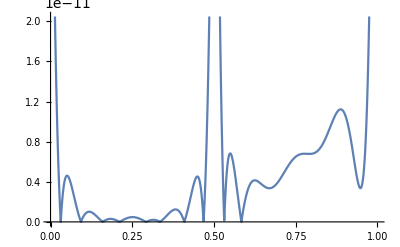

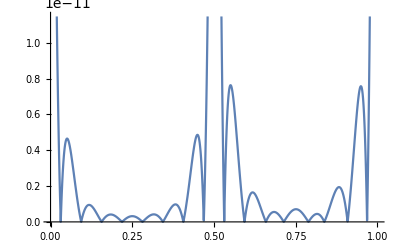

(1. | -1.
1.20517 | -1.00517
1.4214 | -1.0214
1.64986 | -1.04986
1.89182 | -1.09182
2.14872 | -1.14872
2.42212 | -1.22212
2.71375 | -1.31375
3.02554 | -1.42554
3.3596 | -1.5596)

(5.69726×10^-11
5.0826×10^-13
1.76748×10^-13
1.0747×10^-13
7.3852×10^-13
9.20424×10^-11
2.81331×10^-12
4.16511×10^-12
6.79812×10^-12
1.07572×10^-11)

(5.71746×10^-11
4.49196×10^-13
3.01759×10^-13
3.05089×10^-13
4.64961×10^-13
9.42688×10^-11
8.09797×10^-13
3.58602×10^-13
2.73337×10^-13
1.1231×10^-12)

```mathematica
Remove["Global`*"];
ψ[ii_,jj_,x_]:=Module[{},
nh=2ii-1;
Return[Piecewise[{{√(jj+1/2)2^(k/2)LegendreP[jj,2^k x-nh],(nh-1)/2^k≤ x<(nh+1)/2^k}}]];
];
Ψ[x_]:=Flatten[Table[ψ[i,j,x],{i,1,2^(k-1)},{j,0,M-1}]];
DD[P_]:=Module[{},
If[P==0,Return[IdentityMatrix[M*2^(k-1)]]];
H=Table[0,{i,M},{j,M}];
For[r=2,r≤ M,r++,
For[s=1,s≤ r-1,s++,
If[Mod[r+s,2]≠0,
H⟦r,s⟧=2^k √((2r-1)(2s-1));
];
];
];
Return[ArrayFlatten[Table[If[i==j,MatrixPower[H,P],0],{i,1,2^(k-1)},{j,1,2^(k-1)}]]];
];
Q[P_]:=Module[{},
X=W=Table[0,{i,1,M},{j,1,M}];
W ⟦1,1⟧=2;
X⟦1,1⟧=1;X⟦M,M⟧=1;
For[i=1,i< M,i++,
X⟦i,i+1⟧=1/(√(2i-1))1/(√(2i+1));
X⟦i+1,i⟧=-1/(√(2i-1))1/(√(2i+1));
];
Return[MatrixPower[1/2^k ArrayFlatten[Table[If[i==j,X,If[i<j,W,0]],{i,1,2^(k-1)},{j,1,2^(k-1)}]],P]];
];
β[Ι_,S_]:=Module[{ii=Ι,ss=S},
Return[A⟦ii⟧.DD[ss].Ψ[0]];
];

(***************************)
M=8;k=2;
l=2;p=2;
y0={{1,2},{-1,0}};
yreal[t_]={t+ⅇ^t,t-ⅇ^t};
AA=1/π∫_0^1 yreal[x]⟦1⟧Ψ[x]ⅆx ;
BB= ∫_0^1 yreal[x]⟦2⟧Ψ[x]ⅆx ;
x0=Join[AA,BB];
(***************************)
 CC=Flatten[Table[Subscript[c, i,j],{i,1,2^(k-1)},{j,0,M-1}]];
A=Table[Flatten[Table[Subscript[a, o,i,j],{i,1,2^(k-1)},{j,0,M-1}]],{o,1,l}];

ans0=Flatten[Simplify[Table[β[i,j]-y0⟦i,j+1⟧,{i,1,l},{j,0,p-1}]]];
(******************)
U[x_]=Integrate[Integrate[{1-1/3 t^3-1/2(A⟦2⟧.DD[1].Ψ[t])^2,-1+t^2-t A⟦1⟧.Ψ[t]},{t,0,x},Assumptions->0≤ x ≤ 1]/.x->t,{t,0,x},Assumptions->0≤ x ≤ 1];
V[x_]=Integrate[Integrate[{
1/2 Integrate[ (A⟦1⟧.Ψ[t])^2+( A⟦2⟧.Ψ[t])^2,{t,0,x},Assumptions->0≤ x ≤ 1]/.x->t,
1/4 Integrate[ (A⟦1⟧.Ψ[t])^2-( A⟦2⟧.Ψ[t])^2,{t,0,x},Assumptions->0≤ x ≤ 1]/.x->t
},{t,0,x},Assumptions->0≤ x ≤ 1]/.x->t,{t,0,x},Assumptions->0≤ x ≤ 1];
eq[x_]=Table[-A⟦i⟧.Ψ[x]+∑_(s=0)^(p-1) y0[[i,s+1]] x^s+U[x]⟦i⟧+V[x]⟦i⟧,{i,1,l}];
xx=Table[(2r-1)/(2^k M),{r,1,2^(k-1)M}];
ANSWER=Table[,{i,1, 2^(k-1)M}];
For[i=1,i≤ 2^(k-1)M,i++,
ANSWER⟦i⟧=eq[xx⟦i⟧];
]; 
javab=Flatten[A]/.FindRoot[Simplify[Flatten[ANSWER]]==0 ,Table[{Flatten[A]⟦i⟧,x0⟦i⟧},{i,1,Length[Flatten[A]]}],MaxIterations->150];
yr1[x_]=Simplify[javab⟦1;;2^(k-1)M⟧.Ψ[x]]
yr2[x_]=Simplify[javab⟦2^(k-1)M+1;;2^(k-1)M*l⟧.Ψ[x]]
Plot[{Abs[yreal[t]⟦1⟧-Re[yr1[t]]]},{t,0,1}]
Plot[{Abs[yreal[t]⟦2⟧-Re[yr2[t]]]},{t,0,1}]
Table[{Round[yr1[i],10^-5],Round[yr2[i],10^-5]},{i,0,0.9,0.1}]//N//MatrixForm
Table[Abs[yr1[i]-yreal[i]⟦1⟧],{i,0,0.9,0.1}]//N//MatrixForm
Table[Abs[yr2[i]-yreal[i]⟦2⟧],{i,0,0.9,0.1}]//N//MatrixForm
```